```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Tru_Tm.txt","Table"];
```

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Pmgood[k_]:=If[k<0.0001||k>1.993,0,Pm[k]];
Trgood[k_]:=If[k<1.9755223192*^-7||k>12.477498542,0,tr[k]];
```

```mathematica
kvals=Union[Range[0.001,0.4,0.001],Range[0.4,1,0.03]];
Dimensions[kvals]
```

{420}

```mathematica
t1=#^3/(2*Pi^2)*term1[#,Pmgood]&/@kvals;
t2=#^3/(2*Pi^2)*term2[#,Pmgood]&/@kvals;
t3=#^3/(2*Pi^2)*term3[#,Pmgood,Trgood]&/@kvals;
t4=#^3/(2*Pi^2)*term4[#,Pmgood,Trgood]&/@kvals;
t5=#^3/(2*Pi^2)*term5[#,Pmgood,Trgood]&/@kvals;
```

Suave::success: Needed 40000 function evaluations on 40 subregions.

Suave::success: Needed 29000 function evaluations on 29 subregions.

Suave::success: Needed 15000 function evaluations on 15 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 19000 function evaluations on 19 subregions.

Suave::success: Needed 15000 function evaluations on 15 subregions.

Suave::success: Needed 16000 function evaluations on 16 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 29000 function evaluations on 29 subregions.

Suave::success: Needed 21000 function evaluations on 21 subregions.

Suave::success: Needed 17000 function evaluations on 17 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

```mathematica
Export["~/jennaproject/data/kvals.txt",kvals];
Export["~/jennaproject/data/b2b2.txt",t1];
Export["~/jennaproject/data/b1b2.txt",t2];
Export["~/jennaproject/data/b1br.txt",t3];
Export["~/jennaproject/data/b2br.txt",t4];
Export["~/jennaproject/data/brbr.txt",t5];
```

```mathematica
Dimensions[t1]
Dimensions[t2]
Dimensions[t3]
Dimensions[t4]
Dimensions[t5]
Dimensions[kvals]
```

{420}

{420}

{420}

«3 more identical outputs»

```mathematica
Plin=Pmgood[#]&/@kvals;
```

```mathematica
Export["~/jennaproject/data/plin.txt",Plin];
```

```mathematica
kvals
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.43,0.46,0.49,0.52,0.55,0.58,0.61,0.64,0.67,0.7,0.73,0.76,0.79,0.82,0.85,0.88,0.91,0.94,0.97,1.}

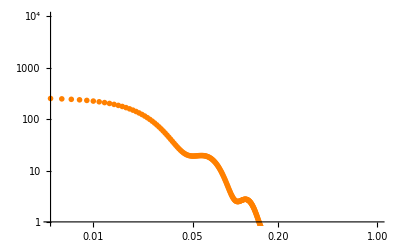

```mathematica
γ3=ListLogLogPlot[Thread[{kvals,Abs[t5]/h^3}],PlotRange->{{0.005,1},{1,10^4}},PlotMarkers-> {mark3, .02}]
```